```mathematica
ClearAll["Global`*"];
```

```mathematica
ϵ=10^-5;znak=5;n=2; (*Размерность пространства R^n*)

X0={-1,-2};η=1; f[{x_,y_}]:=η(x^2-y)^2+(x-1)^2;

(*X0={0,√10};f[{x_,y_}]:=11 x^2+3 y^2+6x y-2 √10(x-3y)-22;(*X0={√10,0};X0={0,√10};*)*)

L=2;(*длина ребра*) 

For[i=1,i≤n+1,i++,For[j=1,j≤n,j++,(*определение координат вершин симплекса S1*)
If[j<i-1,Subscript[x, j]=X0[[j]];];
If[j==i-1,Subscript[x, j]=X0[[j]]+L √(j/(2(j+1)));];
If[j>i-1,Subscript[x, j]=X0[[j]]-L/(√(2j(j+1)));];
];
Subscript[X, i]={Subscript[x, 1],Subscript[x, 2]}
];
 X={Table[Subscript[X, i],{i,1,n+1}]};Versh=Map[f, X[[1]]];iFunk=3;
δ=1/3(*Коэф редукции*); α=1;β=3;γ=1/2;
k=1;(*кол-во симплексов*)
While[(*True*)L>ϵ,
Flag=True;(*не отсортировано?*)
While[Flag,Flag=False;(*правильная нумерация вершин симплекса(сортировка)*)
For[j=1,j≤n,j++,If[Versh[[j]]>Versh[[j+1]],
vspom1=Versh[[j]];Versh[[j]]=Versh[[j+1]];Versh[[j+1]]=vspom1;
vspom2=  X[[k,j]]; X[[k,j]]= X[[k,j+1]]; X[[k,j+1]]=vspom2;Flag=True;];];];
Versh=N[Versh,20];X=N[X,20];
Xc=1/n∑_(i=1)^n X[[k,i]];
vspom1=f[Xc];iFunk++;
(*If[N[1/(n+1)∑_(i=1)^(n+1) (Versh[[i]]-vspom1)^2,20]<ϵ^2,Break[];];*)
vspom2=Xc+α (Xc -X[[k,n+1]]);(*Отражение координат максимальной вершины*)
vspom1=f[vspom2];
iFunk++;

(*If[vspom1<Versh[[1]],change=Xc+β (vspom2-Xc ); iFunk++; vspom3=f[change];If[vspom3<Versh[[1]],vspom2=change; vspom1=vspom3;];]; (*РАСТЯЖЕНИЕ*)

If[(vspom1<=Versh[[n+1]]) &&(vspom1>Versh[[n]]) ,change=Xc+γ (vspom2-Xc ); iFunk++; vspom3=f[change];If[vspom3<=Versh[[n+1]],vspom2=change; vspom1=vspom3;];];(*СЖАТИЕ*)

If[vspom1>Versh[[n+1]],change=Xc+γ (Versh[[n+1]]-Xc ); iFunk++; vspom3=f[change];If[vspom3<=Versh[[n+1]],vspom2=change; vspom1=vspom3;];];(*СЖАТИЕ*)*)

If[vspom1≥Versh[[n+1]] ,(*Возвращение с Редукцией*)
L*= δ;
For[i=2,i≤n+1,i++,Subscript[X, i]=X[[k,1]]+δ(X[[k,i]]-X[[k,1]])];Subscript[X, 1]=X[[k,1]];
X=Append[X,Table[Subscript[X, i],{i,1,n+1}]];k++;
Versh={Versh[[1]],f[X[[k,2]]],f[X[[k,3]]]};iFunk+=2;
Continue[];
];
Subscript[X, n+1]=vspom2;
For[i=1,i≤n,i++,Subscript[X, i]=X[[k,i]]];
X=Append[X,Table[Subscript[X, i],{i,1,n+1}]];k++;
Versh={Versh[[1]],Versh[[2]],vspom1};
];
"Результат получен за "<>ToString[Length[X]]<> " итерации."
"Точка минимума X^* = "
SetAccuracy[N[X[[k,1]],znak],znak]
"Минимальное значение функции: f(X^*) = "
SetAccuracy[N[f[X[[k,1]]],znak],znak]
"Количество обращений к функции :"
iFunk
```

Результат получен за 65 итерации.

Точка минимума X^* =

{0.9863,0.9667}

Минимальное значение функции: f(X^*) =

0.0002

Количество обращений к функции :

155

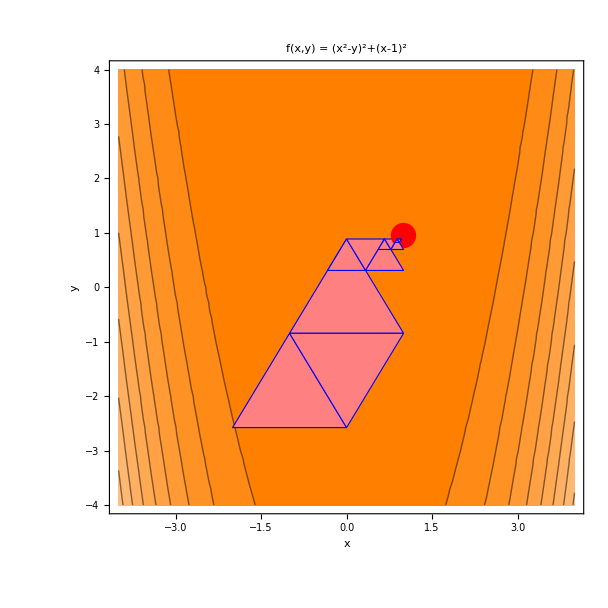

```mathematica
(*отрисовываем топографию целевой функции*)
x1=-4;y1=-4; x2=4; y2=4;(*квадратичная*)
(*x1=-4;y1=-4; x2=4; y2=4;(*розенброк*)*)
(*отрисовываем топографию целевой функции*)Show[ContourPlot[f[{x,y}],{x,x1,x2},{y,y1,y2},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5 #]],Lighter[Orange,0.5 #]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->700],(*отрисовываем массив симплексов*)Table[Graphics[{FaceForm[Pink],EdgeForm[Directive[Thick,Dashed,Blue]],Polygon[X[[i]]]}],{i,1,Length[X]}],Graphics[{Red,PointSize[0.03],Point[X[[k,1]]]}]](*отрисовываем найденную точку минимума*)
```